```mathematica
(*
test data
*)
```

```mathematica
kttests=Import["C:\\Users\\taoji\\OneDrive - UCSF\\Desktop\\test movies\\Book1.xlsx"];
```

```mathematica
imgcrop[pic_]:=ImageCrop[pic,IntegerPart[Min[ImageDimensions[pic]]*0.7]];
```

```mathematica
kt1list={"D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_1.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_2.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_3.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_4.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_5.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_6.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_7.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_8.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_9.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_10.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_11.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_12.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_13.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_14.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_15.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_16.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_17.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_18.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_19.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_20.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_21.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_22.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_23.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_24.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_25.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_26.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_27.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_28.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_29.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_30.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_31.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_32.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_33.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_34.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_35.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_36.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_37.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_38.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_39.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_40.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_41.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_42.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_43.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_44.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_45.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_46.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_47.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_48.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_49.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_50.tif","D:\\combine0802\\control\\d1c1control0707 done\\ch1\\3.-1\\Path from Track_1 to Track_1.tifcroppedimages\\(+-1)\\SUM_Path from Track_1 to Track_1-1.tif_51.tif"};
```

```mathematica
kt2list={"D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_1.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_2.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_3.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_4.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_5.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_6.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_7.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_8.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_9.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_10.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_11.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_12.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_13.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_14.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_15.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_16.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_17.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_18.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_19.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_20.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_21.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_22.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_23.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_24.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_25.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_26.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_27.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_28.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_29.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_30.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_31.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_32.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_33.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_34.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_35.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_36.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_37.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_38.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_39.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_40.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_41.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_42.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_43.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_44.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_45.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_46.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_47.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_48.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_49.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_50.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_51.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_52.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_53.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_54.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_55.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_56.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_57.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_58.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_59.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_60.tif","D:\\combine0802\\control\\dic1(0714\\ch1\\14.-23\\Path from Track_23 to Track_23.tifcroppedimages\\(+-1)\\SUM_Path from Track_23 to Track_23-1.tif_61.tif"};
```

```mathematica
kt3list={"D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_1.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_2.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_3.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_4.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_5.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_6.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_7.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_8.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_9.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_10.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_11.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_12.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_13.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_14.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_15.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_16.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_17.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_18.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_19.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_20.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_21.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_22.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_23.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_24.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_25.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_26.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_27.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_28.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_29.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_30.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_31.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_32.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_33.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_34.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_35.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_36.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_37.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_38.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_39.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_40.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_41.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_42.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_43.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_44.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_45.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_46.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_47.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_48.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_49.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_50.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_51.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_52.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_53.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_54.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_55.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_56.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_57.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_58.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_59.tif","D:\\combine0802\\control\\new(2)(1)\\ch1\\2.-11\\Path from Track_11 to Track_11.tifcroppedimages\\(+-1)\\SUM_Path from Track_11 to Track_11-1.tif_60.tif"};
```

```mathematica
kt4list={"D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_1.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_2.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_3.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_4.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_5.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_6.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_7.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_8.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_9.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_10.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_11.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_12.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_13.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_14.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_15.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_16.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_17.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_18.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_19.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_20.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_21.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_22.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_23.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_24.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_25.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_26.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_27.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_28.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_29.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_30.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_31.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_32.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_33.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_34.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_35.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_36.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_37.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_38.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_39.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_40.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_41.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_42.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_43.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_44.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_45.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_46.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_47.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_48.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_49.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_50.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_51.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_52.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_53.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_54.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_55.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_56.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_57.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_58.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_59.tif","D:\\combine0802\\control\\new(2)(1) -new\\ch1\\14.-10\\Path from Track_10 to Track_10.tifcroppedimages\\(+-1)\\SUM_Path from Track_10 to Track_10-1.tif_60.tif"};
```

```mathematica
kt1images=imgcrop/@Import/@kt1list
kt2images=imgcrop/@Import/@kt2list
kt3images=imgcrop/@Import/@kt3list
kt4images=imgcrop/@Import/@kt4list
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Transpose[{kt1images,ImageAdjust/@kt1images}]
Transpose[{kt2images,ImageAdjust/@kt2images}]
Transpose[{kt3images,ImageAdjust/@kt3images}]
Transpose[{kt4images,ImageAdjust/@kt4images}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
(*
tests run
*)
```

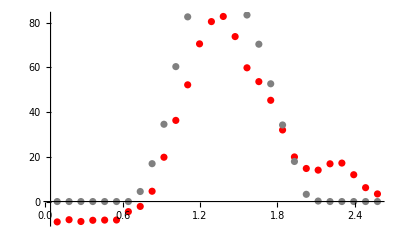
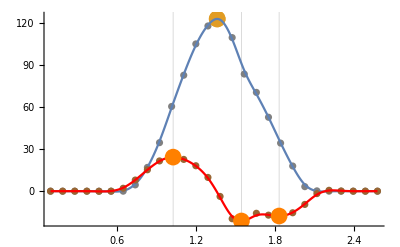
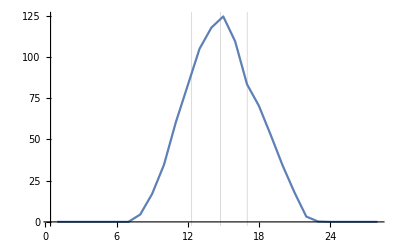
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
allplots[-Graphics-,r]
```